```mathematica
ξ= 31;
h = 0.67810;
Mpc = 1.029 10^14 s;
τ[k_]:= ξ/k;
```

```mathematica
τ[0.001 h/Mpc]
τ[10 h/Mpc]
```

4.70417×10^18 s

4.70417×10^14 s

```mathematica
H0 = 67.66 km/s/Mpc;
km = 3.240779289 10^-20 Mpc;
Ωr = 8.24 10^-5;
Ωm=0.3111;
ΩΛ=0.6889;
η[z0_]:=1/H0 NIntegrate[1/(√(Ωr+Ωm a + ΩΛ a^4)),{a,0,1/(1+z)}]/. z-> z0;
zmν[mν_]:=1890mν-1;
```

```mathematica
zmν[0.02]
```

36.8

NIntegrate::nlim: a = 1/(1.+z) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

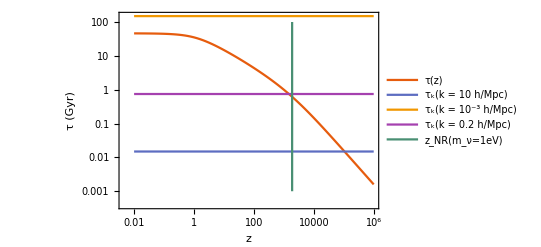

149.122

```mathematica
s = 3.17 10^-17 Gyr;
Gyr = 1;
dat = Table[{10^logz,η[10^logz]},{logz,-2,6,0.1}];
τ1 = {{10^-2,τ[10 h/Mpc]},{10^6,τ[10 h/Mpc]}};
τ2 = {{10^-2,τ[0.001 h/Mpc]},{10^6,τ[0.001 h/Mpc]}};
τ3 = {{10^-2,τ[0.2 h/Mpc]},{10^6,τ[0.2 h/Mpc]}};
m1 = {{zmν[1],10^-3},{zmν[1],10^2}};
ListLogLogPlot[{dat,τ1,τ2,τ3,m1},Joined->True, PlotTheme-> "Scientific",FrameLabel-> {"z","τ (Gyr)"},PlotLegends->{"τ(z)","τ_k(k = 10 h/Mpc)","τ_k(k = 10^-3 h/Mpc)","τ_k(k = 0.2 h/Mpc)","z_NR(m_ν=1eV)"}]
τ[0.001 h/Mpc]
Clear[s]
```

From this I understand that, τ_k (k = 10h/Mpc) corresponds to redshift z = 10^5, which corresponds to a mass m_⋁=53 eV. 
Also from this, τ_k (k = 0.2h/Mpc) corresponds to a redshift z ~ 3000, which is the NR transition of a neutrino of mass m_ν=1eV. 
So, all modes larger than k = 0.2h/Mpc (k < 0.2h/Mpc) are still being computed exactly (totally or partially) in the period where the neutrinos should transition to NR.

Of course, if we change the approximation onset from 31 to 1, then the fluid approximation begins earlier, and the first mode that enters the fluid approximation in the time of interest is k = 0.006 h/Mpc.
Also, τ_k(k= 10^-3 h/Mpc) = 149Gyr has not happened yet, so it is impossible for this mode to enter the fluid approximation (xd), it is always computed exactly.

```mathematica
mν[z_]:=(1+z)/1890.;(* eV*)
```